```mathematica
Assuming[r>0&&kJ>z>0,1/r*Integrate[-k*kJ^2/(kJ^2-k^2)*Sin[k*r],{k,0,z}]]
```

1/(2 r)kJ^2 (-CosIntegral[-kJ r] Sin[kJ r]+CosIntegral[kJ r] Sin[kJ r]+CosIntegral[r (-kJ+z)] Sin[kJ r]-CosIntegral[r (kJ+z)] Sin[kJ r]-Cos[kJ r] SinIntegral[r (kJ-z)]+Cos[kJ r] SinIntegral[r (kJ+z)])

```mathematica
(1/(2 r)kJ^2 (-CosIntegral[-kJ r] Sin[kJ r]+CosIntegral[kJ r] Sin[kJ r]+CosIntegral[r (-kJ+z)] Sin[kJ r]-CosIntegral[r (kJ+z)] Sin[kJ r]-Cos[kJ r] SinIntegral[r (kJ-z)]+Cos[kJ r] SinIntegral[r (kJ+z)]))/.{kJ->1,z->0.1}
```

1/(2 r)(-CosIntegral[-r] Sin[r]+CosIntegral[-0.9 r] Sin[r]+CosIntegral[r] Sin[r]-CosIntegral[1.1 r] Sin[r]-Cos[r] SinIntegral[0.9 r]+Cos[r] SinIntegral[1.1 r])

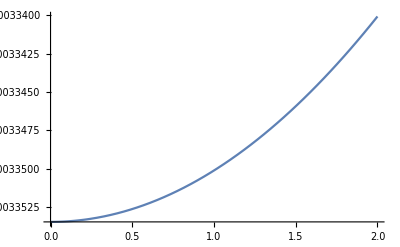

```mathematica
Plot[1/(2 r)(-CosIntegral[-r] Sin[r]+CosIntegral[-0.9 r] Sin[r]+CosIntegral[r] Sin[r]-CosIntegral[1.1 r] Sin[r]-Cos[r] SinIntegral[0.9 r]+Cos[r] SinIntegral[1.1 r]),{r,0,2}]
```

```mathematica
(1/(2 r)kJ^2 (-CosIntegral[-kJ r] Sin[kJ r]+CosIntegral[kJ r] Sin[kJ r]+CosIntegral[r (-kJ+z)] Sin[kJ r]-CosIntegral[r (kJ+z)] Sin[kJ r]-Cos[kJ r] SinIntegral[r (kJ-z)]+Cos[kJ r] SinIntegral[r (kJ+z)]))/.{kJ->1,z->0.95}
```

1/(2 r)(-CosIntegral[-r] Sin[r]+CosIntegral[-0.05 r] Sin[r]+CosIntegral[r] Sin[r]-CosIntegral[1.95 r] Sin[r]-Cos[r] SinIntegral[0.05 r]+Cos[r] SinIntegral[1.95 r])

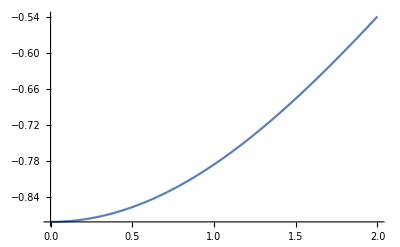

```mathematica
Plot[1/(2 r)(-CosIntegral[-r] Sin[r]+CosIntegral[-0.050000000000000044 r] Sin[r]+CosIntegral[r] Sin[r]-CosIntegral[1.95 r] Sin[r]-Cos[r] SinIntegral[0.050000000000000044 r]+Cos[r] SinIntegral[1.95 r]),{r,0,2}]
```

```mathematica
Assuming[r>0&&kJ>0,1/r*Integrate[-k*kJ^2/(kJ^2-k^2)*Sin[k*r],{k,0,∞},PrincipalValue->True]]
```

(kJ^2 π Cos[kJ r])/(2 r)